# Classification of geometric data

## Comparison of decision trees and naive Bayesian classifiers

Anton Antonov
MathematicaForPrediction at WordPress
MathematicaForPrediction at GitHub
MathematicaVsR at GitHub
October 2013
June 2017 (completed and redone for DHOxSS-2017)

## Mission statement

With this notebook we demonstrate and explain couple of fundamental Machine learning algorithms over simple to understand geometric data. (Mixed numerical and categorical.)

This notebook is taken from MathematicaForPrediction at GitHub.

## Introduction

This notebook is for walk-through examples and demonstrations of the classifiers Decision tree and Naive Bayes.

For more details of building NBC see [5]. For another comparison of Decision trees and Naive Bayes see [6].
SUPERVISED

### Package load

These commands load the packages [1,2,3] used in this notebook:

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/AVCDecisionTreeForest.m"]
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/NaiveBayesianClassifier.m"]
```

### Random seed

For reproducibility we do a random seed set .

```mathematica
SeedRandom[264]
```

## Geometric data: coordinates and color

Generate few thousand random 2D points, assign a color to each of them, and then select points that are marked “liked” according to some simple predicate. The colors are given as strings so they are amenable for classification.

```mathematica
(* random 2D points *)
n=2000;
pnts=RandomReal[{0,1},{n,2}];
pntColors={"Red","Blue","Green"}⟦#⟧&/@RandomInteger[{1,3},n];
```

```mathematica
(* simple predicate *)
liked=MapThread[(#1=="Red"||#1=="Green")&&(#2⟦1⟧>0.7||#2⟦2⟧>0.8)&,{List@@@pntColors,pnts},1];
liked=If[#,"liked","not liked"]&/@liked;
```

Form a xyColorData array of point coordinates and colors.

```mathematica
xyColorData=Flatten/@Transpose[{pnts,pntColors,liked}];
```

Plot the xyColorData array.

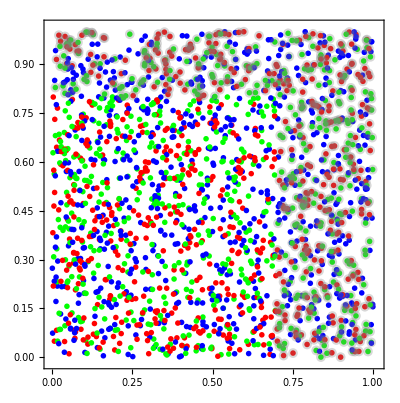

```mathematica
(* plot the xyColorData array *)
Graphics[{PointSize[0.01],MapThread[{ToExpression[#1],Point[#2]}&,{xyColorData⟦All,3⟧,xyColorData⟦All,1;;2⟧}],Gray,Opacity[0.3],Map[Disk[#1,0.015]&,Pick[xyColorData⟦All,1;;2⟧,#=="liked"&/@xyColorData⟦All,-1⟧]]},Frame->True,ImageSize->400]
AutoCollapse[]
```

A sample of the xyColorData array rows looks like this:

```mathematica
Magnify[#,0.8]&@TableForm[xyColorData⟦100;;112⟧,TableHeadings->{Automatic,Style[#,Blue,FontFamily->"Times"]&/@{"X-Coord","Y-Coord","Color","Liked"}}]
AutoCollapse[]
```

| X-Coord | Y-Coord | Color | Liked
1 | 0.577646 | 0.57204 | Red | not liked
2 | 0.0205879 | 0.632906 | Red | not liked
3 | 0.653 | 0.696322 | Green | not liked
4 | 0.013149 | 0.914429 | Red | liked
5 | 0.526332 | 0.00787627 | Green | not liked
6 | 0.483128 | 0.491971 | Blue | not liked
7 | 0.271171 | 0.505256 | Green | not liked
8 | 0.120085 | 0.380995 | Green | not liked
9 | 0.263575 | 0.538949 | Blue | not liked
10 | 0.864297 | 0.123233 | Blue | not liked
11 | 0.522412 | 0.914163 | Red | liked
12 | 0.14065 | 0.662624 | Green | not liked
13 | 0.346286 | 0.326844 | Red | not liked

Here is the summary:

```mathematica
RecordsSummary[xyColorData]
```

{1 column 1
Min | 0.000208206
1st Qu | 0.233141
Median | 0.486671
Mean | 0.489319
3rd Qu | 0.746018
Max | 0.999929,2 column 2
Min | 0.000247694
1st Qu | 0.245783
Mean | 0.501416
Median | 0.506137
3rd Qu | 0.751681
Max | 0.999517,3 column 3
Green | 678
Blue | 668
Red | 654,4 column 4
not liked | 1427
liked | 573}

Here is an alternative summary view:

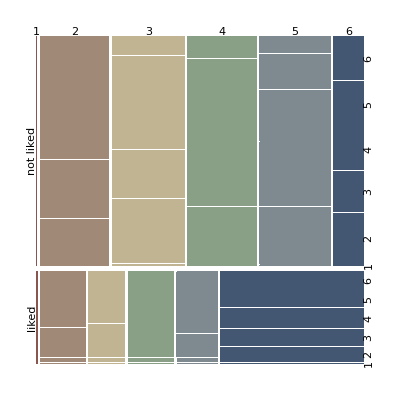

```mathematica
MosaicPlot[ToCategoricalColumns[Reverse/@xyColorData⟦All,{1,2,-1}⟧]]
```

## More complicated geometric xyColorData: coordinates, color, and shape

Create random points and assign randomly colors and letters (shapes) to them.

```mathematica
n=2000;
pnts=RandomReal[{0,1},{n,2}];
pntColors={"Red","Blue","Green"}⟦#⟧&/@RandomInteger[{1,3},n];
pntShapes={"a","b","c","d","e"}⟦#⟧&/@RandomInteger[{1,5},n];
```

Determining the labels (“liked” and “not liked”) for each point: 
1. blue and green points with the shapes “c” and “e” and for which y/x<0.8 are liked; 2. red and green points with the shapes “a” and “d” and x>0.7 or y>0.8 are liked.

```mathematica
liked=MapThread[(((#2=="Blue"||#2=="Green")&&(#3=="c"||#3=="e")&&#1⟦2⟧/#1⟦1⟧<0.8)||((#2=="Red"||#2=="Green")&&(#1⟦1⟧>0.7||#1⟦2⟧>0.8)&&(#3=="a"||#3=="d")))&,{pnts,List@@@pntColors,pntShapes},1];
liked=If[#,"liked","not liked"]&/@liked;
```

Combined the points coordinates, colors, shapes, and labels into a xyColorData array.

```mathematica
xyColorShapeData=Flatten/@Transpose[{pnts,pntColors,pntShapes,liked}];
```

Here is an excerpt of the xyColorData array:

```mathematica
Magnify[#,0.8]&@TableForm[xyColorShapeData⟦100;;112⟧,TableHeadings->{Automatic,Style[#,Blue,FontFamily->"Times"]&/@{"X-Coord","Y-Coord","Color","Shape","Liked"}}]
AutoCollapse[]
```

| X-Coord | Y-Coord | Color | Shape | Liked
1 | 0.390021 | 0.27407 | Blue | a | not liked
2 | 0.637737 | 0.0740239 | Blue | a | not liked
3 | 0.362975 | 0.385255 | Green | b | not liked
4 | 0.909676 | 0.952722 | Blue | e | not liked
5 | 0.129587 | 0.917682 | Green | d | liked
6 | 0.0508657 | 0.15931 | Red | b | not liked
7 | 0.367642 | 0.441544 | Blue | e | not liked
8 | 0.712679 | 0.0631042 | Green | b | not liked
9 | 0.884106 | 0.867212 | Green | a | liked
10 | 0.30572 | 0.0375437 | Red | b | not liked
11 | 0.594453 | 0.0777193 | Green | d | not liked
12 | 0.818525 | 0.0304095 | Blue | e | liked
13 | 0.672036 | 0.961338 | Red | a | liked

```mathematica
RecordsSummary[xyColorShapeData]
```

{1 column 1
Min | 0.000675136
1st Qu | 0.248794
Mean | 0.495102
Median | 0.496148
3rd Qu | 0.737266
Max | 0.999966,2 column 2
Min | 0.0000617151
1st Qu | 0.244654
Mean | 0.493202
Median | 0.496032
3rd Qu | 0.734193
Max | 0.999991,3 column 3
Green | 673
Red | 669
Blue | 658,4 column 4
b | 413
c | 403
e | 400
d | 394
a | 390,5 column 5
not liked | 1560
liked | 440}

Plot the points with their colors and shapes. The points with the label “liked” have disks around them. The first set of liked points is transparent blue disks, the second set of points is with transparent pink disks.

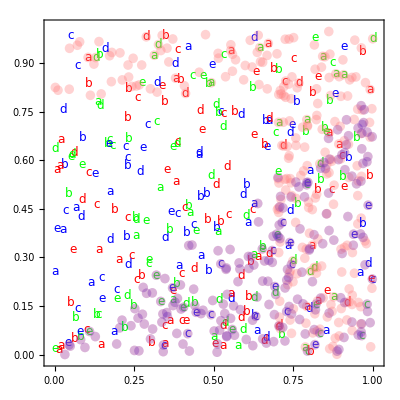

```mathematica
Graphics[{PointSize[0.01],MapThread[{#2,Text[Style[#3,FontSize->12],#1]}&,{pnts,ToExpression/@pntColors,pntShapes}],
Pink,Opacity[0.35],Map[Disk[#1,0.015]&,Pick[pnts,#=="liked"&/@liked]],
Blue,Opacity[0.15],Map[Disk[#1,0.015]&,Pick[pnts,MapThread[#1=="liked"&&(#2=="c"||#2=="e")&,{liked,pntShapes}]]]},Frame->True,ImageSize->400]
AutoCollapse[]
```

## Decision trees

### Decision tree building

First we assign the data of interest to a generic variable:

```mathematica
data=xyColorData;
```

This variable is for splitting data into a training part and a testing part:

```mathematica
trainingDataLength=600;
```

Build a decision tree:

```mathematica
dtree=BuildDecisionTree[data⟦1;;trainingDataLength⟧,1,"ImpurityFunction"->"Entropy","Strata"->100,"LinearCombinations"->{"Rank"->0}]
```

{{0.147612,Blue,3,Symbol,600},{{{202,not liked}}},{{0.32122,0.700729,1,Number,398},{{0.511937,0.799381,2,Number,283},{{{224,not liked}}},{{{59,liked}}}},{{{115,liked}}}}}

In order to visualize the decision tree, make node-to-node rules it.

```mathematica
trules=DecisionTreeToRules[dtree];
```

Here is how the node-to-node rules look like:

```mathematica
trules//ColumnForm
```

{{0.147612,Blue,3,Symbol,600,node 0}→leaf 0
202 | not liked,= Blue}
{{0.147612,Blue,3,Symbol,600,node 0}→{0.32122,0.700729,1,Number,398,node 1},≠ Blue}
{{0.32122,0.700729,1,Number,398,node 1}→{0.511937,0.799381,2,Number,283,node 2},≤ 0.7}
{{0.32122,0.700729,1,Number,398,node 1}→leaf 1
115 | liked,> 0.7}
{{0.511937,0.799381,2,Number,283,node 2}→leaf 2
224 | not liked,≤ 0.8}
{{0.511937,0.799381,2,Number,283,node 2}→leaf 3
59 | liked,> 0.8}

Now we can visualize the decision tree with GraphPlot and LayeredGraphPlot. As it was explained above each non-leaf node has the form

{impurity measure, splitting value, column index, variable type, number of records}

Each leaf node is a list of pairs, each pair is {_Integer, label}.

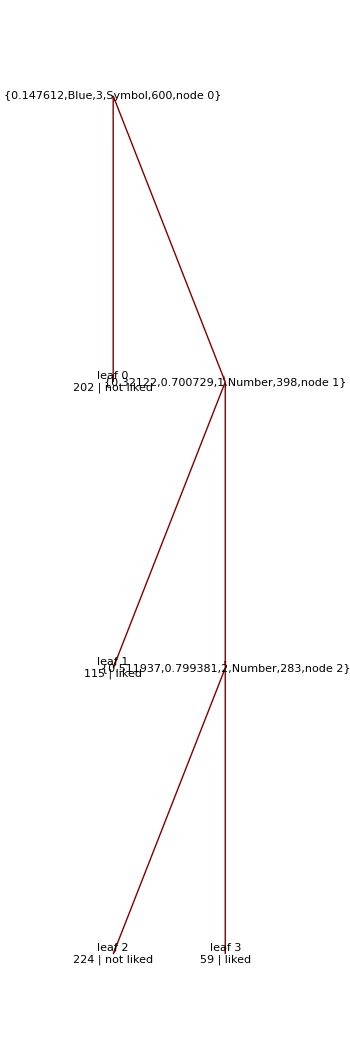

```mathematica
LayeredGraphPlot[trules,DirectedEdges->True,VertexLabeling->True,ImageSize->350]
```

Note that for the simple data xyColorData the decision tree has guessed correctly the predicate.

### Classification with the decision tree

After we have obtained the decision tree using the training xyColorData we can test its classification capabilities with test xyColorData. Given a decision tree dtree the classification is done with the function DecisionTreeClassify:

```mathematica
xyColorData⟦trainingDataLength+3⟧
```

{0.0972976,0.874164,Blue,not liked}

```mathematica
DecisionTreeClassify[dtree,xyColorData⟦trainingDataLength+3⟧]
```

{{202,not liked}}

DecisionTreeClassify returns a leaf node of the decision tree with which the classification is made. We can take the label of the first element of the classification result:

```mathematica
%⟦1,2⟧
```

not liked

Let us compute the classification results for all rows in the test xyColorData

```mathematica
guesses=DecisionTreeClassify[dtree,#]⟦1,2⟧&/@xyColorData⟦601;;-1⟧;
```

And compare them with the actual labels in the test rows

```mathematica
comparisons=MapThread[Equal,{guesses,data⟦601;;-1,-1⟧}];
Count[comparisons,True]
Count[comparisons,False]
```

1400

0

It is a good idea to know what is the success ratio of the classification for each label. Often in practice the some of the labels are represented in small fractions of xyColorData.

```mathematica
Count[data⟦trainingDataLength+1;;-1,-1⟧,"liked"]/Length[data⟦trainingDataLength+1;;-1⟧]//N
```

0.285

```mathematica
resRules=DecisionTreeClassificationSuccess[dtree,data⟦trainingDataLength+1;;-1⟧]
```

{{liked,True}→1.,{liked,False}→0.,{not liked,True}→1.,{not liked,False}→0.,{All,True}→1.,{All,False}→0.}

Here is tabulation of the results

```mathematica
Block[{labels={"liked","not liked",All},gridData},
gridData=Outer[{#1,#2}/.resRules&,labels,{True,False}];
gridData=MapThread[Prepend,{gridData,labels}];
Grid[Prepend[gridData,Style[#,Blue,FontFamily->"Times"]&/@{"Label","Fraction of\ncorrect guesses","Fraction of\nincorrect guesses"}],Alignment->Left,Dividers->{{False,True,False},{False,True,False}}]
]
AutoCollapse[]
```

Label | Fraction of
correct guesses | Fraction of
incorrect guesses
liked | 1. | 0.
not liked | 1. | 0.
All | 1. | 0.

### Using the built-in decision tree forest classifier

Let us repeat the above calculations with the built-in “RandomForest” classifier.

```mathematica
data=xyColorShapeData;
```

This makes the classifier:

```mathematica
cf=Classify[Map[Most[#]->Last[#]&,data⟦1;;600⟧],Method->"RandomForest"]
```

ClassifierFunction[…]

This calculates a classifier measurements object over the test data:

```mathematica
cm=ClassifierMeasurements[cf,Map[Most[#]->Last[#]&,data⟦601;;-1⟧]]
```

ClassifierMeasurementsObject[…]

Let us see some classifier evaluation metrics of with that object:

```mathematica
cm[{"Accuracy","Precision","Recall"}]
```

{0.961429,<|liked→0.98893,not liked→0.954827|>,<|liked→0.840125,not liked→0.997225|>}

```mathematica
Dataset[MapThread[Append,{cm[{"TruePositiveRate","FalsePositiveRate"}],{"All"->#,"All"->1-#}&@cm["Accuracy"]}]]
```

Dataset[<>]

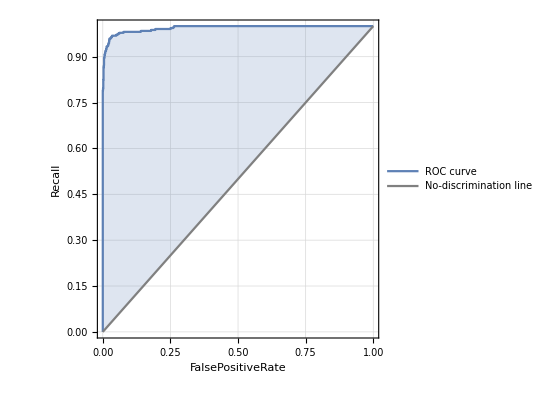
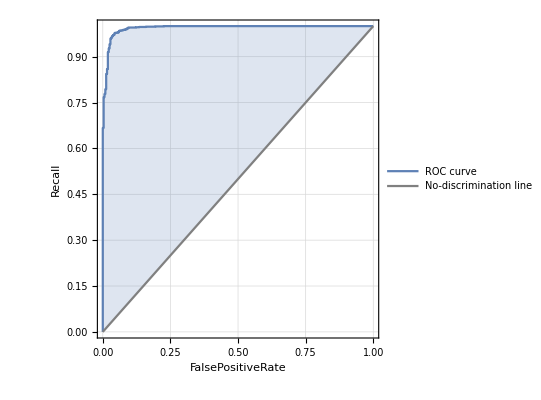
{<|liked→-Graphics-,not liked→-Graphics-|>}

```mathematica
cm[{"ROCCurve"}]
```

## Naive Bayesian classifiers

### Naive Bayesian classifier building

For more details of building NBC see [5]. (Here we just code...)

```mathematica
nbcRules=MakeBayesianClassifiers[data⟦1;;trainingDataLength⟧,10];
Magnify[nbcRules,0.6]
```

{liked→(0.201667 Times@@MapThread[#1[#2]&,{{Piecewise[{{0.279362, 0≤#1<1/10}, {0.396694, 1/10≤#1<1/5}, {0.236128, 1/5≤#1<3/10}, {0.850059, 3/10≤#1<2/5}, {0.667514, 2/5≤#1<1/2}, {0.79693, 1/2≤#1<3/5}, {0.698405, 3/5≤#1<7/10}, {2.39384, 7/10≤#1<4/5}, {2.13736, 4/5≤#1<9/10}, {1.84735, 9/10≤#1<1}, {0, True}}]&,Piecewise[{{1.65289, 0≤#1<1/10}, {1.62707, 1/10≤#1<1/5}, {1.13093, 1/5≤#1<3/10}, {1.00854, 3/10≤#1<2/5}, {0.540947, 2/5≤#1<1/2}, {0.393546, 1/2≤#1<3/5}, {0.708383, 3/5≤#1<7/10}, {0.303593, 7/10≤#1<4/5}, {1.02322, 4/5≤#1<9/10}, {1.35237, 9/10≤#1<1}, {0, True}}]&,Piecewise[{{0.708383, #1==Red}, {0.854126, #1==Blue}, {1.44946, #1==Green}, {0, True}}]&,Piecewise[{{1.27258, #1==a}, {1.34538, #1==c}, {1.09259, #1==e}, {1.24975, #1==d}, {0, True}}]&},#1}]&),not liked→(0.798333 Times@@MapThread[#1[#2]&,{{Piecewise[{{1.18204, 0≤#1<1/10}, {1.1524, 1/10≤#1<1/5}, {1.19296, 1/5≤#1<3/10}, {1.03788, 3/10≤#1<2/5}, {1.08399, 2/5≤#1<1/2}, {1.0513, 1/2≤#1<3/5}, {1.07619, 3/5≤#1<7/10}, {0.647902, 7/10≤#1<4/5}, {0.712692, 4/5≤#1<9/10}, {0.785951, 9/10≤#1<1}, {0, True}}]&,Piecewise[{{0.835073, 0≤#1<1/10}, {0.841597, 1/10≤#1<1/5}, {0.966927, 1/5≤#1<3/10}, {0.997842, 3/10≤#1<2/5}, {1.11596, 2/5≤#1<1/2}, {1.1532, 1/2≤#1<3/5}, {1.07367, 3/5≤#1<7/10}, {1.17592, 7/10≤#1<4/5}, {0.994135, 4/5≤#1<9/10}, {0.910989, 9/10≤#1<1}, {0, True}}]&,Piecewise[{{1.03685, #1==Blue}, {0.886462, #1==Green}, {1.07367, #1==Red}, {0, True}}]&,Piecewise[{{0.936911, #1==d}, {0.912754, #1==c}, {0.931143, #1==a}, {0.976611, #1==e}, {1.25261, #1==b}, {0, True}}]&},#1}]&)}

```mathematica
{lf,nlf}={"liked"/.nbcRules,"not liked"/.nbcRules};
```

Next let us plot the NBC’s probability functions that correspond to the variables.

```mathematica
factor=lf⟦1,1⟧;
funcs=Cases[lf,_Piecewise,∞];
funcs=Table[With[{f=factor,fun=funcs⟦i⟧},f*fun&],{i,Length[funcs]}];
```

```mathematica
funcs⟦3⟧
```

0.201667 (Piecewise[{{0.708383, #1==Red}, {0.854126, #1==Blue}, {1.44946, #1==Green}, {0, True}}])&

```mathematica
nbcPlots=Table[
If[NumberQ[data⟦1,ind⟧],Plot[funcs⟦ind⟧[x],{x,Min[data⟦All,ind⟧],Max[data⟦All,ind⟧]},PlotRange->{All,{0,1.02}},PlotStyle->Thickness[0.005],Frame->True,FrameLabel->Map[Style[#,Larger]&,{"x",TraditionalForm[P[Row[{"high"," / ",Subscript[X, ind]==x}]]]}],Axes->False,PlotLabel->Style[({"X","Y","Color","Liked"}⟦ind⟧),Larger],GridLines->Automatic,ImageSize->500],
(*ELSE*)
BarChart[funcs⟦ind⟧/@Union[data⟦All,ind⟧],ChartLabels->Placed[Union[data⟦All,ind⟧],Below],Frame->True,GridLines->Automatic,ImageSize->500]
],{ind,Range[1,4]}];
```

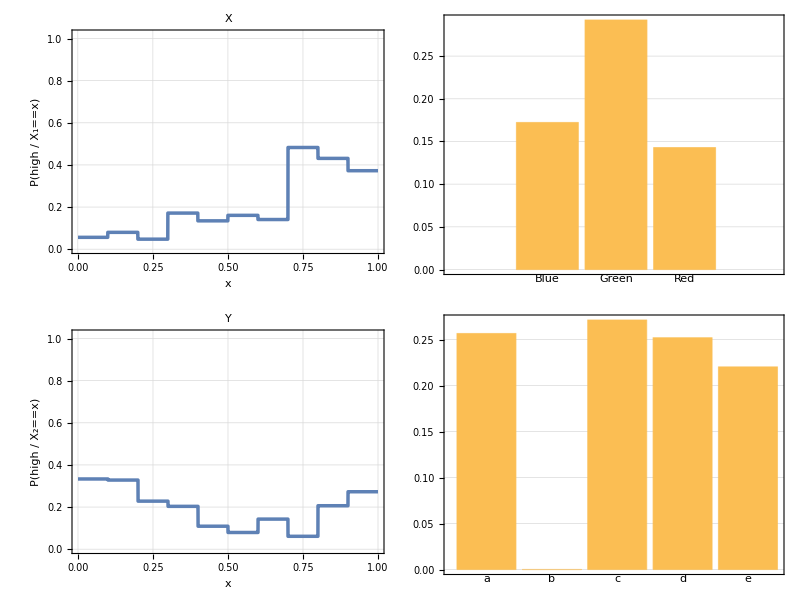

```mathematica
Multicolumn[Magnify[#,0.7]&/@nbcPlots,2]
```

### Classification the naive Bayesian classifier

```mathematica
res=NBCClassify[{lf,"liked"},{nlf,"not liked"},0.5,0.8,Most[#],All]&/@data⟦trainingDataLength+1;;-1⟧;
res⟦1;;12⟧
```

{not liked,not liked,not liked,not liked,not liked,not liked,not liked,not liked,not liked,not liked,not liked,not liked}

```mathematica
resRules=NBCClassificationSuccess[NBCClassify[{lf,"liked"},{nlf,"not liked"},0.5,0.8,#]&,data⟦trainingDataLength+1;;-1⟧]
```

{{liked,True}→0.304075,{liked,False}→0.695925,{not liked,True}→0.955597,{not liked,False}→0.0444033,{All,True}→0.807143,{All,False}→0.192857}

The resulting rules are interpreted with the following table construction:

```mathematica
Block[{labels={"liked","not liked",All},gridData},
gridData=Outer[{#1,#2}/.resRules&,labels,{True,False}];
gridData=MapThread[Prepend,{gridData,labels}];
Grid[Prepend[gridData,Style[#,Blue,FontFamily->"Times"]&/@{"Label","Fraction of\ncorrect guesses","Fraction of\nincorrect guesses"}],Alignment->Left,Dividers->{{False,True,False},{False,True,False}}]
]
AutoCollapse[]
```

Label | Fraction of
correct guesses | Fraction of
incorrect guesses
liked | 0.304075 | 0.695925
not liked | 0.955597 | 0.0444033
All | 0.807143 | 0.192857

### Using the built-in naive Bayesian classifier

Let us repeat the above calculations with the built-in “RandomForest” classifier.

```mathematica
data=xyColorShapeData;
```

This makes the classifier:

```mathematica
cf=Classify[Map[Most[#]->Last[#]&,data⟦1;;trainingDataLength⟧],Method->"NaiveBayes"]
```

ClassifierFunction[…]

This calculates a classifier measurements object over the test data:

```mathematica
cm=ClassifierMeasurements[cf,Map[Most[#]->Last[#]&,data⟦trainingDataLength+1;;-1⟧]]
```

ClassifierMeasurementsObject[…]

Let us see some classifier evaluation metrics of with that object:

```mathematica
cm[{"Accuracy","Precision","Recall"}]
```

{0.805,<|liked→0.649351,not liked→0.824238|>,<|liked→0.31348,not liked→0.950046|>}

```mathematica
Dataset[MapThread[Append,{cm[{"TruePositiveRate","FalsePositiveRate"}],{"All"->#,"All"->1-#}&@cm["Accuracy"]}]]
```

Dataset[<>]

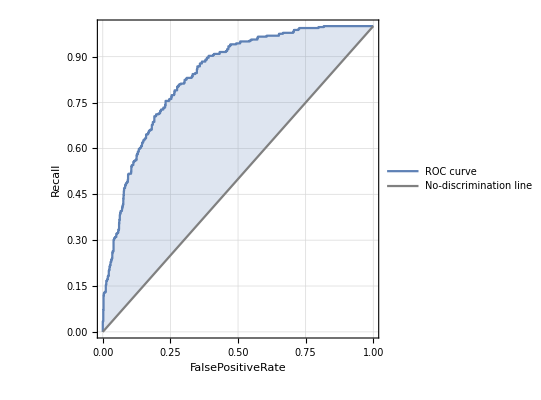
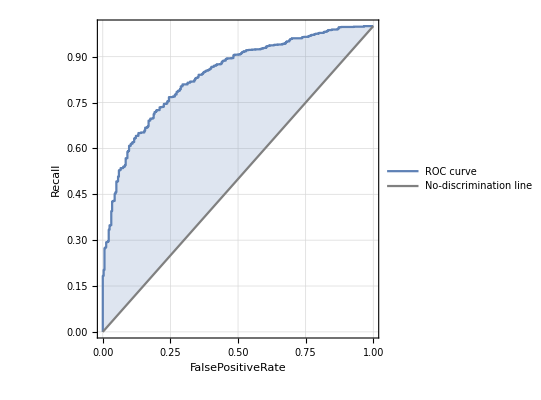
{<|liked→-Graphics-,not liked→-Graphics-|>}

```mathematica
cm[{"ROCCurve"}]
```

We  see the results with the built-in NBC are much worse than with the built-in Random forest classification algorithm.

## References

[1] Anton Antonov, MathematicaForPrediction utilities, (2014), source code MathematicaForPrediction at GitHub, package MathematicaForPredictionUtilities.m.

[2] Anton Antonov, Decision tree and random forest implementations in Mathematica, (2013), source code MathematicaForPrediction at GitHub,  https://github.com/antononcube/MathematicaForPrediction, package AVCDecisionTreeForest.m.

[3] Anton Antonov, Implementation of naive Bayesian classifier generation in Mathematica, (2013), source code at MathematicaForPrediction at GitHub, , https://github.com/antononcube/MathematicaForPrediction, package NaiveBayesianClassifier.m.

[4] Anton Antonov, “Waveform recognition with decision trees”, (2013),  MathematicaForPrediction at GitHub, https://github.com/antononcube/MathematicaForPrediction.

[5] Anton Antonov, “Generation of Naive Bayesian Classifiers”, (2013), MathematicaForPrediction at WordPress.
   URL: https://mathematicaforprediction.wordpress.com/2013/10/18/generation-of-naive-bayesian-classifiers/ .

[6] Anton Antonov, “Classification and association rules for census income data”, (2014), MathematicaForPrediction at WordPress.com , URL: https://mathematicaforprediction.wordpress.com/2014/03/30/classification-and-association-rules-for-census-income-data/ .